```mathematica
(* Generate figure for article "Precautionary Saving and Precautionary Wealth" with Miles Kimball for Palgrave Dictionary of Economics and Finance, 2nd Ed. *)
(* http://econ.jhu.edu/people/ccarroll/PalgravePrecautionary.pdf *)
```

```mathematica
(* This cell is basically housekeeping and setup stuff; it can be ignored *)
ClearAll["Global`*"];ParamsAreSet=False;
If[$VersionNumber<8,(*then*) Print["These programs require Mathematica version 8 or greater."];Abort[]];
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
rootDir = SetDirectory["../../.."];
AutoLoadDir=SetDirectory["./Mathematica/CoreCode/Autoload"];Get["./init.m"];
CoreCodeDir=SetDirectory[".."];
rootDir = SetDirectory[".."];
Get[CoreCodeDir<>"/MakeAnalyticalResults.m"];
Get[CoreCodeDir<>"/VarsAndFuncs.m"];
(* Method of creating figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
Get[CoreCodeDir<>"/ParametersBase.m"];
```

```mathematica
Get[CoreCodeDir<>"/ParametersBase.m"];
𝓂Max=2.5 𝓂E;
𝔤=𝔤Base=-0.02;
℧=0.005; ϑ=0.25; r =0.2; CheckForΓImpatience; CheckForRImpatience;FindStableArm;
```

Solving ...

Below 𝓂MinPermitted after 379 backwards Euler iterations.

Last 2 Points:(1.84025 | 0.975917 | 0.293452 | -5.05279 | -0.1169
1.58696 | 0.897307 | 0.329614 | -5.34156 | -0.172868)

Solving ...

Above 𝓂MaxPermitted after 633 backwards Euler iterations.

Last 2 Points:(28.7149 | 6.0796 | 0.18377 | -0.895968 | -0.0000199266
28.8524 | 6.10488 | 0.183767 | -0.892262 | -0.0000196241)

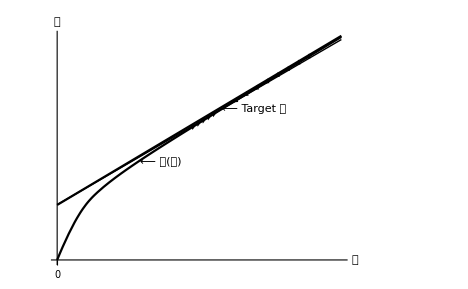

```mathematica
(*$TextStyle={FontFamily->"Courier",FontSize->9};*)ArrowListBelow=Table[Arrow[{mPlot-0.05,cE[mPlot-0.05]},{mPlot,cE[mPlot]},HeadScaling->Automatic,HeadLength->0.01,HeadWidth->1.5],{mPlot,𝓂E-1.25,𝓂E-0.25,0.25}];
ArrowListAbove=Table[Arrow[{mPlot+0.05,cE[mPlot+0.05]},{mPlot,cE[mPlot]},HeadScaling->Automatic,HeadLength->0.01,HeadWidth->1.5],{mPlot,𝓂E+4,𝓂E+0.5,-0.5}];
If[$VersionNumber>=6
,ArrowListBelow=Table[{Arrowheads[0.02],Arrow[{{mPlot-0.05,cE[mPlot-0.05]},{mPlot,cE[mPlot]}}]},{mPlot,𝓂E-1.25,𝓂E-0.25,0.25}];
ArrowListAbove=Table[{Arrowheads[0.02],Arrow[{{mPlot+0.05,cE[mPlot+0.05]},{mPlot,cE[mPlot]}}]},{mPlot,𝓂E+4,𝓂E+0.5,-0.5}]];

𝒸PFPlot=Plot[cEPF[m],{m,0,𝓂Max},PlotStyle->Black];
𝓂EDelEqZeroPlot=Plot[𝓂EDelEqZero[m],{m,0,𝓂Max},DisplayFunction->Identity];
𝒸LowerPlot=Plot[cE[m],{m,0,𝓂Max},PlotStyle->Black];
PalgraveTargetPlot=Show[𝒸PFPlot,𝓂EDelEqZeroPlot,𝒸LowerPlot,Graphics[Text[" ⟵ Target 𝓂",{𝓂E,𝒸E},{-1,0}]],Graphics[Text[" ⟵ Perm Inc",{2 𝓂E,𝓂EDelEqZero[2 𝓂E]},{-1,0}]],Graphics[Text["Perf Foresight \!\(\*OverscriptBox[\(𝒸\), \(-\)]\)(𝓂) ⟶  ",{2 𝓂E,cEPF[2 𝓂E]},{1,0}]],Graphics[Text[" ⟵ 𝒸(𝓂)",{0.5 𝓂E,cE[0.5 𝓂E]},{-1,0}]],Graphics[ArrowListBelow],Graphics[ArrowListAbove]
,Ticks->{{{0,"0"}},None},AxesLabel->{"𝓂","𝒸"}
,PlotRange->{{0,𝓂Max},{0,cEPF[𝓂Max]}}
,AxesOrigin->{0.,0.}]
```

```mathematica
SetDirectory["/Volumes/Data/Papers/PalgravePrecautionary/PalgravePrecautionary-Latest/Figures/"]
Export["PalgraveTargetPlot.eps",PalgraveTargetPlot,"EPS"];
Export["PalgraveTargetPlot.pdf",PalgraveTargetPlot,"PDF"];Export["PalgraveTargetPlot.png",PalgraveTargetPlot,"PNG"];Export["PalgraveTargetPlot.svg",PalgraveTargetPlot,"SVG"];
```

/Volumes/Data/Papers/PalgravePrecautionary/PalgravePrecautionary-Latest/Figures